## Increasing graphs

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/blmayer/repos/thesis/article-2

```mathematica
Get[ParentDirectory[]<>"/visibility.wl"]
```

```mathematica
Get[ParentDirectory[]<>"/sdl.wl"]
```

```mathematica
gDistance[g_]:=Block[{res},
res=0;
Do[
Do[res=res+GraphDistance[g, s,e],{e,VertexList[g]}],
{s,VertexList[g]}
];
Return[res/(Length@VertexList[g](Length@VertexList[g]-1))]
]
```

```mathematica
linksToJson[fileName_,links_]:=Block[{},
Export[NotebookDirectory[]<>fileName<>".json",Table[{x[[1]],x[[2]]},{x,links}]];
]
```

```mathematica
linkCases[links_]:=Block[{},
<|
"EvenEven"->Length@Select[links,EvenQ[#[[1]]]&&EvenQ[#[[2]]]&],
"OddOdd"->Length@Select[links,OddQ[#[[1]]]&&OddQ[#[[2]]]&],
"EvenOdd"->Length@Select[links,EvenQ[#[[1]]]&&OddQ[#[[2]]]&],
"OddEven"->Length@Select[links,OddQ[#[[1]]]&&EvenQ[#[[2]]]&]
|>
]
```

## Divisors

```mathematica
Col
```

```mathematica
len=30000;
```

```mathematica
series=Table[{x,Length@Divisors[x]},{x,len}];
```

```mathematica
Max[series[[All,2]]]
```

96

```mathematica
Cases[PrimeQ/@Range[30000],True]//Length
```

3245

```mathematica
Max[series[[All,2]]]
```

6

```mathematica
Select[series,EvenQ@#[[2]]&]//Length
```

29827

```mathematica
series=Table[{x,orbit[x]},{x,len}];
```

```mathematica
Select[series,EvenQ@#[[2]]&]//Length
```

9462

```mathematica
sdl[series[[All,2]]]
```

{0.973266,0.581753}

## Visibility graphs

```mathematica
divsNVLinksTable=Import[NotebookDirectory[]<>"divs-nv-links-50k.json"]
```

{{1,2},{835,836},{2,3},{2,4},{836,837},{836,839},{836,840},{3,4},{837,838},{837,839},{837,840},{4,5},{4,6},{5,6},{838,839},{838,840},{6,7},{6,8},{6,12},145758,{49158,49160},{49159,49160},{49160,49161},{49160,49162},{49160,49164},{49161,49162},{49161,49164},{49162,49163},{49162,49164},{49163,49164},{49164,49165},{49164,49166},{49164,49168},{49164,49170},{49165,49166},{49166,49167},{49166,49168},{49166,49170}}
 |  |  |  |

```mathematica
divsNVLinks=Table[x[[1]]<->x[[2]],{x,divsNVLinksTable}]
```

{1<->2,835<->836,2<->3,2<->4,836<->837,836<->839,836<->840,3<->4,837<->838,837<->839,837<->840,4<->5,4<->6,5<->6,838<->839,838<->840,6<->7,6<->8,6<->12,839<->840,840<->841,840<->842,145751,49156<->49157,49156<->49158,49157<->49158,49158<->49159,49158<->49160,49159<->49160,49160<->49161,49160<->49162,49160<->49164,49161<->49162,49161<->49164,49162<->49163,49162<->49164,49163<->49164,49164<->49165,49164<->49166,49164<->49168,49164<->49170,49165<->49166,49166<->49167,49166<->49168,49166<->49170}
 |  |  |  |

```mathematica
gDistance[divsNVGraph]
```

$Aborted

```mathematica
MeanGraphDistance[divsNVGraph]
```

## Natural Visibility

```mathematica
divsNVLinks=naturalVisibility[series];
```

```mathematica
linksToJson["divs-nv-links-30k.json", divsNVLinks]
```

```mathematica
linkCases[divsNVLinks]
```

```mathematica
<|"EvenEven"->37399,"OddOdd"->2973,"EvenOdd"->23145,"OddEven"->23128|>/Length@divsNVLinks//N
```

<|EvenEven→0.431635,OddOdd→0.0343124,EvenOdd→0.267124,OddEven→0.266928|>

```mathematica
divsNVGraph=Graph[divsNVLinks,DirectedEdges->False,VertexLabels->"Name",GraphLayout->"CircularEmbedding"];
```

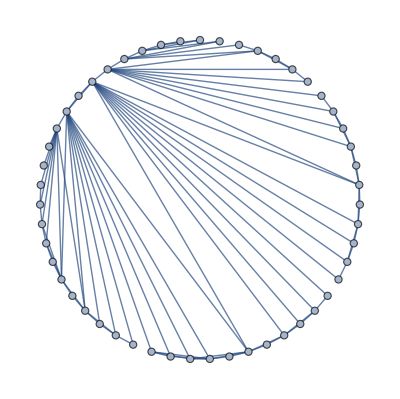

```mathematica
Graph[SortBy[divsNVLinks,First][[;;100]],DirectedEdges->False,GraphLayout->"CircularEmbedding"]
```

```mathematica
divsNVDegrees=Counts[VertexDegree[divsNVGraph]]/Length@VertexDegree[divsNVGraph]
```

<|1→1/50000,3→2503/12500,2→2013/12500,7→2629/50000,4→2293/12500,36→7/10000,5→1527/12500,10→573/25000,11→451/25000,8→1999/50000,17→51/10000,13→267/25000,12→683/50000,26→9/5000,23→23/10000,28→13/12500,34→27/50000,37→11/25000,6→4103/50000,14→29/3125,24→41/25000,9→359/12500,16→311/50000,25→39/25000,18→27/6250,15→77/10000,29→43/50000,21→71/25000,30→27/50000,20→157/50000,27→63/50000,42→1/2500,19→197/50000,22→117/50000,40→7/25000,46→9/50000,31→11/12500,45→1/10000,54→9/50000,33→27/50000,32→3/5000,43→17/50000,49→9/50000,77→1/25000,39→1/3125,41→1/3125,44→13/50000,38→7/25000,35→23/50000,50→7/50000,62→3/50000,47→3/12500,55→1/12500,51→1/10000,52→3/25000,67→1/25000,90→1/50000,61→1/25000,48→1/12500,53→3/50000,56→1/10000,63→1/25000,74→3/50000,93→1/25000,88→1/50000,66→1/25000,57→1/25000,85→1/50000,58→1/50000,76→1/50000,73→1/50000,68→3/50000,59→1/50000,72→1/25000,60→1/50000|>

```mathematica
divsNVDegrees[1]=.
```

```mathematica
data=Table[{x,divsNVDegrees[x]},{x,Keys[divsNVDegrees]}];
divsNVNlm=NonlinearModelFit[data,c k^-γ E^(-d k),{{γ,2},{c,3},{d,0}},k]
```

FittedModel[0.159989 ⅇ^(-0.800424 k) k^2.36626]

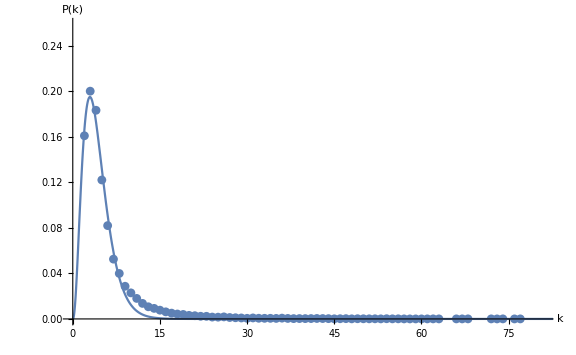

```mathematica
divsNVPlot=Show[
ListPlot[divsNVDegrees,PlotRange->{{0,81},{0,0.259}},AxesOrigin->{0,0}],
Plot[divsNVNlm[x],{x,0,Max[Keys[divsNVDegrees]]},PlotRange->{{0,81},{0,0.26}},AxesOrigin->{0,0}],
AxesLabel-> {Style["k",36, Italic],Style["P(k)", 36,Italic]},LabelStyle->20,ImageSize->Large
]
```

```mathematica
divsNVNlm["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
γ | -2.36626 | 0.131171 | {-2.62781,-2.10471}
c | 0.159989 | 0.00780322 | {0.14443,0.175548}
d | 0.800424 | 0.0344366 | {0.73176,0.869089}

```mathematica
TableForm[Flatten[{"natural visibility",Mean@ VertexDegree[divsNVGraph]//N,MeanGraphDistance[divsNVGraph]//N,
GlobalClusteringCoefficient[divsNVGraph]//N,Mean[divsNVNlm["FitResiduals"]^2],ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@divsNVNlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}],TableHeadings->{{"algo","⟨k⟩","⟨l_min⟩","C_c","⟨e^2⟩","γ","C","δ"}, None},TableDirections->Row]
```

algo | ⟨k⟩ | ⟨l_min⟩ | C_c | ⟨e^2⟩ | γ | C | δ
natural visibility | 5.008 | 5.44117 | 0.352068 | 0.000103855 | -0.864256 ± 0.647733 | 0.377949 ± 0.0792584 | 0.518977 ± 0.176516

## Horizontal Visibility

```mathematica
divsHVLinks=horizontalVisibility[series];
```

```mathematica
linksToJson["divs-hv-links-50k", divsHVLinks]
```

```mathematica
linkCases[divsNVLinks]
```

<|EvenEven→37399,OddOdd→2973,EvenOdd→23145,OddEven→23128|>

```mathematica
divsHVGraph=Graph[divsHVLinks,DirectedEdges->False,VertexLabels->"Name",GraphLayout->"CircularEmbedding"];
```

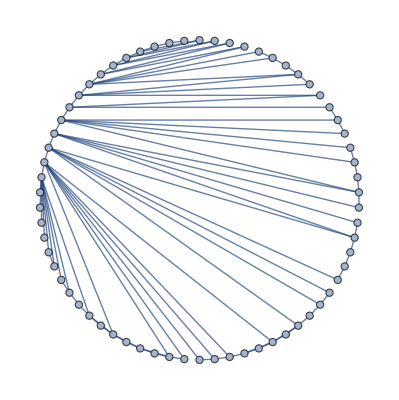

```mathematica
Graph[SortBy[divsHVLinks,First][[;;100]],DirectedEdges->False,GraphLayout->"CircularEmbedding"]
```

```mathematica
divsHVDegrees=Counts[VertexDegree[divsHVGraph]]/Length@VertexDegree[divsHVGraph]
```

<|1→1/50000,2→5583/12500,5→4219/50000,3→2387/12500,19→1/5000,4→649/5000,7→831/25000,12→43/10000,13→141/50000,11→31/5000,6→313/6250,9→763/50000,10→113/12500,8→1087/50000,14→1/500,18→21/50000,15→27/25000,17→27/50000,16→1/1250,23→1/10000,22→1/10000,20→9/50000,21→3/50000,24→1/50000,25→1/50000|>

```mathematica
divsHVDegrees[1]=.
```

```mathematica
data=Table[{x,divsHVDegrees[x]},{x,Keys[divsHVDegrees]}];
divsHVNlm=NonlinearModelFit[data,c k^-γ E^(-d k),{{γ,2},{c,3},{d,0}},k]
```

FittedModel[(1.67472 ⅇ^(-0.135059 k))/k^1.52795]

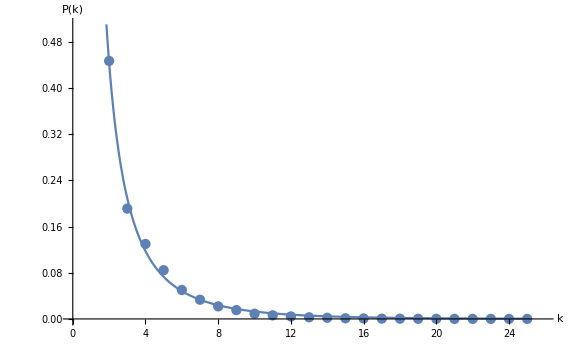

```mathematica
divsHVPlot=Show[
ListPlot[divsHVDegrees,PlotRange->{{0,25.9},{0,.51}},AxesOrigin->{0,0}],Plot[divsHVNlm[x],{x,0,Max[Keys[divsHVDegrees]]},PlotRange->{{0,25},{0,0.51}},AxesOrigin->{0,0}],
AxesLabel-> {Style["k",36, Italic],Style["P(k)", 36,Italic]},LabelStyle->20,ImageSize->Large
]
```

```mathematica
divsHVNlm["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
γ | 1.52795 | 0.156457 | {1.20258,1.85332}
c | 1.67472 | 0.0648899 | {1.53977,1.80967}
d | 0.135059 | 0.0457389 | {0.0399398,0.230178}

```mathematica
TableForm[Flatten[{"horizontal visibility",Mean@ VertexDegree[divsHVGraph]//N,MeanGraphDistance[divsHVGraph]//N,
GlobalClusteringCoefficient[divsHVGraph]//N,Mean[divsHVNlm["FitResiduals"]^2],ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@divsHVNlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}],TableHeadings->{{"algo","⟨k⟩","⟨l_min⟩","C_c","⟨e^2⟩","γ","C","δ"}, None},TableDirections->Row]
```

algo | ⟨k⟩ | ⟨l_min⟩ | C_c | ⟨e^2⟩ | γ | C | δ
horizontal visibility | 3.428 | 9.46032 | 0.279595 | 0.000107087 | 1.76816 ± 0.845097 | 1.87703 ± 0.354401 | 0.0874991 ± 0.251851

## Orbits

```mathematica
orbit[x_]:=Block[{d=0,n=x},
While[n!=Length@Divisors[n],n=Length@Divisors[n];d+=1;];
Return[d]
]
```

```mathematica
orbits=Table[{x,orbit[x]},{x,series[[All,1]]}]
```

{{1,0},{2,0},{3,1},{4,2},{5,1},{6,3},{7,1},{8,3},{9,2},{10,3},{11,1},{12,4},{13,1},{14,3},{15,3},{16,2},{17,1},{18,4},{19,1},{20,4},{21,3},{22,3},{23,1},{24,4},{25,2},49950,{49976,4},{49977,4},{49978,3},{49979,4},{49980,6},{49981,3},{49982,4},{49983,3},{49984,5},{49985,4},{49986,5},{49987,4},{49988,4},{49989,4},{49990,4},{49991,1},{49992,3},{49993,1},{49994,4},{49995,5},{49996,5},{49997,4},{49998,3},{49999,1},{50000,5}}
 |  |  |  |

```mathematica
sdl[orbits[[All,2]]]
```

{0.860937,0.686456}

## Natural Visibility

```mathematica
orbitsNVLinks=naturalVisibility[orbits];
```

```mathematica
linksToJson["orbits-nv-links-50k", orbitsNVLinks]
```

```mathematica
orbitsNVGraph=Graph[orbitsNVLinks,DirectedEdges->False,VertexLabels->"Name",GraphLayout->"CircularEmbedding"];
```

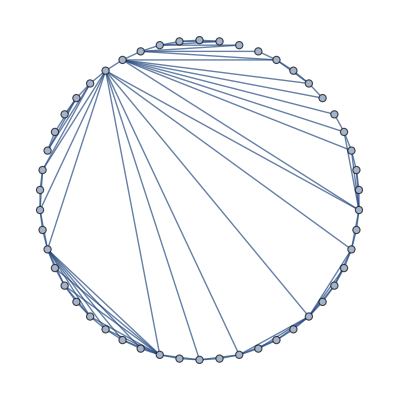

```mathematica
Graph[SortBy[orbitsNVLinks,First][[;;100]],DirectedEdges->False,GraphLayout->"CircularEmbedding"]
```

```mathematica
orbitsNVDegrees=Counts[VertexDegree[orbitsNVGraph]]/Length@VertexDegree[orbitsNVGraph]
```

<|3→10121/50000,2→11981/50000,9→1999/50000,4→9499/50000,11→837/50000,1639→1/50000,5→37/400,7→2659/50000,8→2321/50000,27→1/50000,6→321/5000,10→1319/50000,12→117/12500,14→53/12500,19→7/50000,13→33/5000,25→1/25000,17→23/50000,16→59/50000,15→19/10000,24→1/25000,21→1/12500,18→23/50000,772→1/50000,23→1/25000,340→1/50000,404→1/50000,345→1/50000,20→1/12500,238→1/50000,133→1/25000,175→1/50000,225→1/50000,217→1/50000,185→1/50000,127→1/25000,163→1/50000,62→1/50000,146→3/50000,466→1/50000,480→1/50000,151→1/50000,160→1/50000,100→3/50000,113→1/25000,147→1/50000,205→1/50000,179→1/50000,90→1/50000,174→1/25000,182→1/50000,168→1/50000,125→3/50000,186→1/50000,149→1/25000,162→1/50000,122→1/50000,80→1/25000,94→1/25000,114→1/50000,187→1/50000,204→1/50000,193→1/50000,172→1/50000,84→1/25000,89→1/50000,49→1/25000,77→3/50000,242→1/50000,244→1/50000,181→1/50000,196→1/50000,166→1/50000,136→1/50000,148→1/50000,74→1/12500,69→1/10000,120→1/25000,91→1/25000,71→1/25000,50→3/50000,202→1/50000,213→1/50000,44→1/25000,73→1/25000,128→3/50000,98→3/50000,37→1/50000,60→1/25000,154→1/50000,132→3/50000,96→1/50000,108→1/25000,22→1/50000,61→1/25000,59→1/25000,79→1/50000,52→1/50000,47→1/50000,197→1/50000,223→1/50000,152→1/50000,38→1/25000,70→1/50000,58→1/50000,99→1/12500,102→1/12500,103→3/50000,67→1/25000,123→1/50000,137→1/50000,118→1/50000,106→1/25000,105→1/50000,178→1/50000,81→1/25000,131→1/50000,33→1/25000,88→1/25000,110→1/50000,45→3/50000,55→1/25000,170→1/50000,198→1/50000,54→1/50000,66→1/25000,140→1/50000,121→1/25000,107→1/50000,51→1/25000,64→1/50000,87→1/25000,159→1/25000,101→1/50000,65→1/50000,111→1/25000,26→1/50000,93→1/50000,31→1/50000,53→1/25000,41→1/50000,224→1/50000,130→1/50000,56→1/25000,95→1/25000,75→1/50000,176→1/50000,68→1/50000,117→1/50000,40→1/50000,115→1/50000,139→1/50000,155→1/50000,28→1/50000|>

```mathematica
orbitsNVDegrees[1]=.
```

```mathematica
data=Table[{x,orbitsNVDegrees[x]},{x,Keys[orbitsNVDegrees]}];
orbitsNVNlm=NonlinearModelFit[data,c k^-γ E^(-d k),{γ,c,d},k]
```

FittedModel[0.369219 ⅇ^(-0.49249 k) k^0.812758]

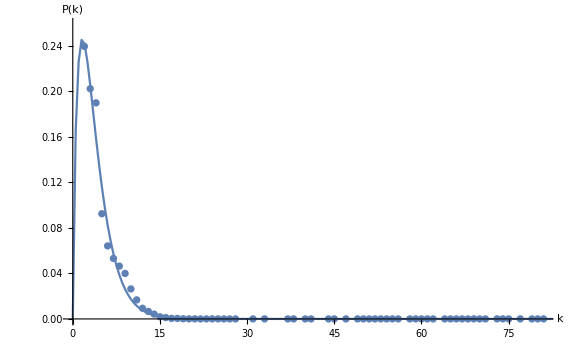

```mathematica
orbitsNVPlot=Show[
ListPlot[orbitsNVDegrees,AxesOrigin->{0,0},PlotRange->{{0,81},{0,0.259}}],Plot[orbitsNVNlm[x],{x,0,Max[Keys[orbitsNVDegrees]]},AxesOrigin->{0,0},PlotRange->{{0,80},{0,0.25}}],
AxesLabel-> {Style["k",36, Italic],Style["P(k)", 36,Italic]},LabelStyle->20,ImageSize->Large
]
```

```mathematica
orbitsNVNlm["ParameterConfidenceIntervalTable"]
```

General::munfl: Exp[-807.191] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

| Estimate | Standard Error | Confidence Interval
γ | -0.812758 | 0.105663 | {-1.02153,-0.60399}
c | 0.369219 | 0.0131965 | {0.343145,0.395293}
d | 0.49249 | 0.028308 | {0.436559,0.548421}

```mathematica
VertexDegree[orbitsNVGraph]//Mean//N
```

5.07516

```mathematica
TableForm[Flatten[{"natural visibility",Mean@ VertexDegree[orbitsNVGraph]//N,MeanGraphDistance[orbitsNVGraph]//N,
GlobalClusteringCoefficient[orbitsNVGraph]//N,Mean[orbitsNVNlm["FitResiduals"]^2],ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@orbitsNVNlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}],TableHeadings->{{"algo","⟨k⟩","⟨l_min⟩","C_c","⟨e^2⟩","γ","C","δ"}, None},TableDirections->Row]
```

algo | ⟨k⟩ | ⟨l_min⟩ | C_c | ⟨e^2⟩ | γ | C | δ
natural visibility | 4.44 | 21.4638 | 0.381986 | 0.000495001 | 0.0786481 ± 1.31562 | 0.592989 ± 0.251989 | 0.323357 ± 0.353352

## Horizontal Visibility

```mathematica
orbitsHVLinks=horizontalVisibility[orbits];
```

```mathematica
linksToJson["orbits-hv-links-50k", orbitsHVLinks]
```

```mathematica
orbitsHVGraph=Graph[orbitsHVLinks,DirectedEdges->False,VertexLabels->"Name",GraphLayout->"CircularEmbedding"];
```

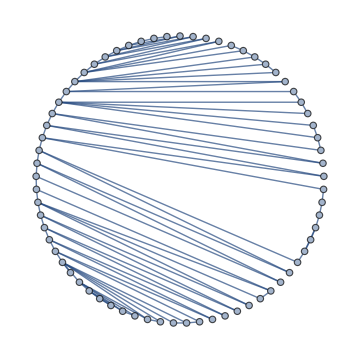

```mathematica
Graph[SortBy[orbitsHVLinks,First][[;;100]],DirectedEdges->False,GraphLayout->"CircularEmbedding",ImageSize->Medium]
```

```mathematica
orbitsHVDegrees=Counts[VertexDegree[orbitsHVGraph]]/Length@VertexDegree[orbitsHVGraph]
```

<|1→1/50000,2→24759/50000,5→4171/50000,3→1411/6250,8→99/50000,4→1497/10000,6→1803/50000,7→179/25000,9→9/12500|>

```mathematica
orbitsHVDegrees[1]=.
```

```mathematica
data=Table[{x,orbitsHVDegrees[x]},{x,Keys[orbitsHVDegrees]}];
orbitsHVNlm=NonlinearModelFit[data,c k^-γ E^(-d k),{γ,c,d},k]
```

FittedModel[(1.87712 ⅇ^(-0.471395 k))/k^0.571288]

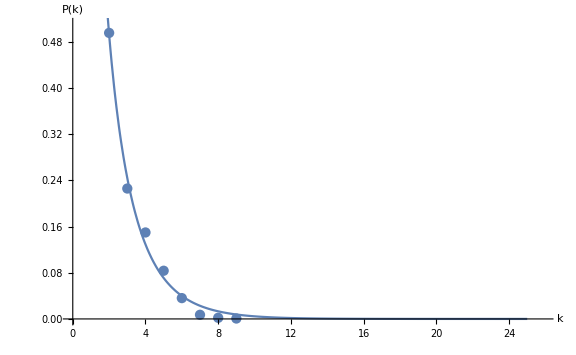

```mathematica
orbitsHVPlot=Show[
ListPlot[orbitsHVDegrees,PlotRange->{{0,25.9},{0,.51}},AxesOrigin->{0,0}],Plot[orbitsHVNlm[x],{x,0,25},PlotRange->{{0,25.9},All},AxesOrigin->{0,0}],
AxesLabel-> {Style["k",36, Italic],Style["P(k)", 36,Italic]},LabelStyle->20,ImageSize->Large
]
```

```mathematica
orbitsHVNlm["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
γ | 0.571288 | 0.673111 | {-1.159,2.30157}
c | 1.87712 | 0.192445 | {1.38242,2.37181}
d | 0.471395 | 0.224219 | {-0.104978,1.04777}

```mathematica
TableForm[Flatten[{"horizontal visibility",Mean@ VertexDegree[orbitsHVGraph]//N,MeanGraphDistance[orbitsHVGraph]//N,
GlobalClusteringCoefficient[orbitsHVGraph]//N,Mean[orbitsHVNlm["FitResiduals"]^2],ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@orbitsHVNlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}],TableHeadings->{{"algo","⟨k⟩","⟨l_min⟩","C_c","⟨e^2⟩","γ","C","δ"}, None},TableDirections->Row]
```

algo | ⟨k⟩ | ⟨l_min⟩ | C_c | ⟨e^2⟩ | γ | C | δ
horizontal visibility | 3.032 | 24.8647 | 0.287817 | 0.000156862 | 0.6107 ± 1.66119 | 1.87882 ± 0.478493 | 0.458558 ± 0.552311

## Final Results

```mathematica
TableForm[{Flatten[{"natural visibility",Mean@ VertexDegree[divsNVGraph]//N,MeanGraphDistance[divsNVGraph]//N,
GlobalClusteringCoefficient[divsNVGraph]//N,Mean[divsNVNlm["FitResiduals"]^2],ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@divsNVNlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}],
Flatten[{"horizontal visibility",Mean@ VertexDegree[divsHVGraph]//N,MeanGraphDistance[divsHVGraph]//N,
GlobalClusteringCoefficient[divsHVGraph]//N,Mean[divsHVNlm["FitResiduals"]^2],ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@divsHVNlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}],Flatten[{"natural visibility",Mean@ VertexDegree[orbitsNVGraph]//N,MeanGraphDistance[orbitsNVGraph]//N,
GlobalClusteringCoefficient[orbitsNVGraph]//N,Mean[orbitsNVNlm["FitResiduals"]^2],ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@orbitsNVNlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}],Flatten[{"horizontal visibility",Mean@ VertexDegree[orbitsHVGraph]//N,MeanGraphDistance[orbitsHVGraph]//N,
GlobalClusteringCoefficient[orbitsHVGraph]//N,Mean[orbitsHVNlm["FitResiduals"]^2],ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@orbitsHVNlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}]},TableHeadings->{None,{"algo","⟨k⟩","⟨l_min⟩","C_c","⟨e^2⟩","γ","C","δ"}}]
```

algo | ⟨k⟩ | ⟨l_min⟩ | C_c | ⟨e^2⟩ | γ | C | δ
natural visibility | 5.008 | 5.44117 | 0.352068 | 0.000103855 | -0.864256 ± 0.647733 | 0.377949 ± 0.0792584 | 0.518977 ± 0.176516
horizontal visibility | 3.428 | 9.46032 | 0.279595 | 0.000107087 | 1.76816 ± 0.845097 | 1.87703 ± 0.354401 | 0.0874991 ± 0.251851
natural visibility | 4.44 | 21.4638 | 0.381986 | 0.000495001 | 0.0786481 ± 1.31562 | 0.592989 ± 0.251989 | 0.323357 ± 0.353352
horizontal visibility | 3.032 | 24.8647 | 0.287817 | 0.000156862 | 0.6107 ± 1.66119 | 1.87882 ± 0.478493 | 0.458558 ± 0.552311